# disLocate - Mathematica Package: (d)etecting (i)ntermolecular (s)tructure (Locate)d at particle positions

## Load the disLocate.m Package into Mathematica:

### 1. Install Package: Menu Bar > File > Install... > Type [Package] Source: [From File...] Name: [disLocate] > [OK]

#### Click the Blue Cell and Press the Two Buttons: “Shift” + “Enter”

```mathematica
<<disLocate`
disLocateVersion
```

1.2017-08-31.thesis-M.v11-final

#### Note: Make sure this line produces a version number before continuing

## Select and Import the Data Files

### 2. Run all Examples by clicking: Menu Bar > Evaluation > Evaluate Entire Notebook

### NOTE: Make sure this notebook is in the same directory as the data folder: micelle_data/

```mathematica
dir=NotebookDirectory[]<>"micelle_data/";
SetDirectory[dir];
```

```mathematica
images={-Graphics-,-Graphics-,-Graphics- ,-Graphics- };
```

```mathematica
xylene2000=Import[dir<>"2000rpm/Result 2000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene4000=Import[dir<>"4000rpm/Result 4000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene6000=Import[dir<>"6000rpm/Result 6000rpm 1um.csv","CSV"][[2;;,3;;4]];
xylene8000=Import[dir<>"8000rpm/Result 8000rpm 1um.csv","CSV"][[2;;,3;;4]];
```

```mathematica
xyXyleneList={xylene2000,xylene4000,xylene6000,xylene8000};
nameList={"2000rpm","4000rpm","6000rpm","8000rpm"};
```

## Voronoi Tessellations - Area Distributions

```mathematica
?PlotVoronoiTessellations
```

PlotVoronoiTessellations[ data2Din_, OptionsPattern[] ]:= Returns a Graphics of the  VoronoiCells[] that has been colour coded to associate disorder metrics to the planar arrangements.  
OptionsPattern=(type→ToString[vor],symmetry→6,cells→{},points→True,scalebar→False,stats→ToString[Count],boundary→ToString[NOEDGE],box→{})

type->ToString[voronoi]=The Main variable that changes the information provided. Option: type→ToString[voronoi] Uses the areas of the Voronoi Cells to calculate an expected hexagonal spacing with the same intensity (shortname ToString[vor]). Option: type→ToString[coordination] Uses the number of facets each individual Voronoi polygon has (shortname ToString[coord]).  Option:  type→ToString[BondOrder] Uses the neighbours -as defined by the Delaunaly Triangulation- to calculate the BondOrderParameter[].  Default symmetry is (symmetry->6) but can be manually set to any variable.

symmetry -> 6 : Sets the symmetry number associated with the BondOrderParameter[]. No effect with any (type).

cells -> {} : This option provides a way to manually pass VoronoiCells[] that have been precalculated.  It is meant to save time by passing the automatic VoronoiCells[] call for a large systems that might be run many times through this function.

points -> True : A graphics option that includes the centroids of the particles on the final plot.  These can be turned off with this option.

scalebar -> False : An option to include the scalebar assocciated with the colour code of (type).

stats -> ToString[Count] : Sets the type of stats passed into VoronoiHistogram[].  Recommended settings - ToString[Count] or ToString[Probability].  See 'hspec' Option for Histogram[].

boundary -> ToString[NoEdge] : Settings for boundary corrections.  Default boundary→ToString[NoEdge] automatically removes any Voronoi Cells that lay on or outside of (box).  Options include: boundary→ToString[periodic] includes edge Voronoi polygons by adding periodically translated neighbours outside of the box (shortname pbc).  boundary→ToString[image] includes edge Voronoi polygons by adding virtual particles that produce Voronoi cells with facets exactly on the edge of (box).  This effectively truncates or clips the edges of the Voronoi cells to the (box). (shortname img).

box -> {} :  Explicitly defines the edges of a box.  Note! - setting a polygon will not change the (boundary), as it will default boundary→ToString[NoEdge] which autodetects the box from the data.  Remember to set a (boundary) option.

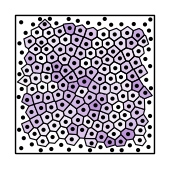
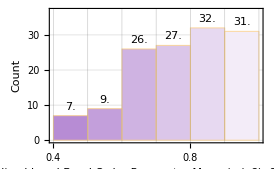

```mathematica
(*  Basic Plot for the Voronoi Tessellation                      *)
(*  Returns the Image of the Tiles and the Histogram of the data *)

PlotVoronoiTessellations@xylene2000
```

```mathematica
(* Export any end result to a pdf file *)
(* A semicolon at the end will supress the output listed in the notebook*)
Export["DisLocate_output.pdf",%];
```

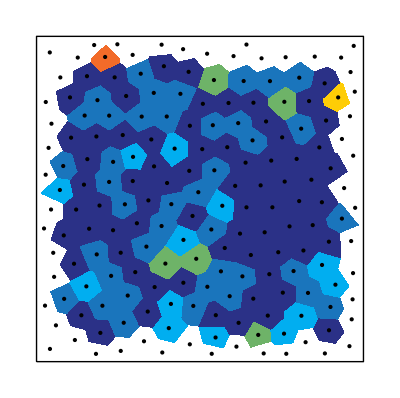
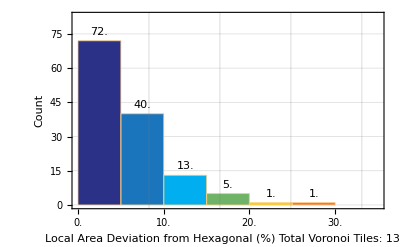
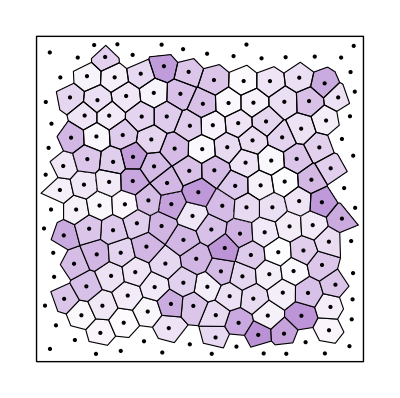
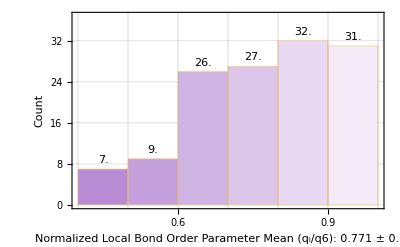
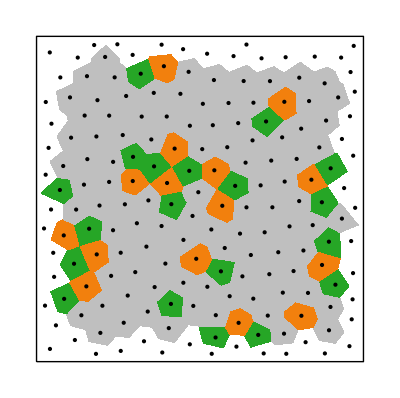
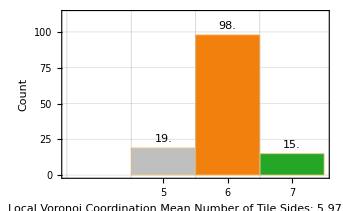

```mathematica
(* Additional Option #1 - type *)
(* Change the colour scheme of the Voronoi Tiles *)

PlotVoronoiTessellations[xylene2000,scalebar->True, type-> #]&/@{"vor","bop","coord"}
```

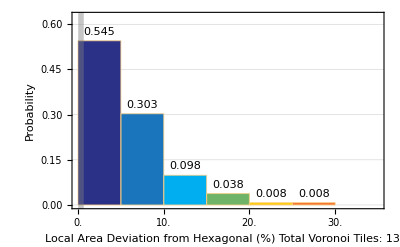
{-Graphics-,-Graphics-}

```mathematica
(* Additional Option #2 - stats *)
(* Instead of Counting the Number of tiles, the Probability can be used. *)

PlotVoronoiTessellations[xylene2000,type-> "vor",stats-> "Probability"]
```

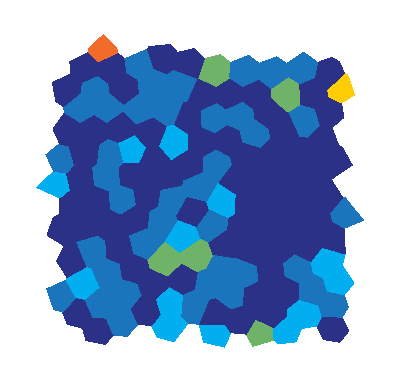
{-Graphics-,-Graphics-}

```mathematica
(* Additional Option #3 - points *)
(* Remove the points and lines to give it a more "stained glass" look *)

PlotVoronoiTessellations[xylene2000,type-> "vor",points-> False]
```

```mathematica
(* Additional Option #4 - raster and scalebar *)
(* a) Change vector graphics to pixelated version - easier to copy/paste *)
(* b) Add the scalebar beside the Voronoi tessellation  *)


PlotVoronoiTessellations[xylene2000,type-> "vor",scalebar->True,raster-> True]
```

{-Graphics-,-Graphics-}

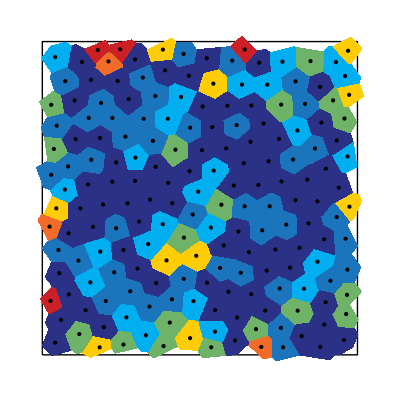
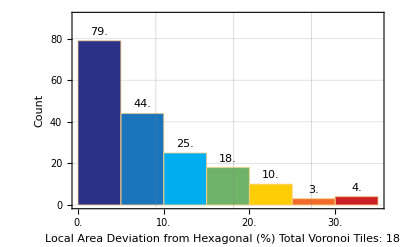
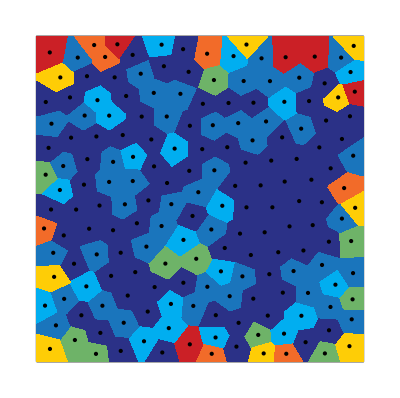
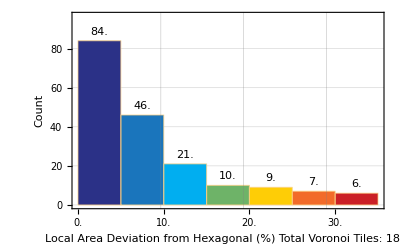
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(* Additional Option #5 - boundary *)
(* Change the routine to sample points outside the edge *)
(* - noedge: removes any tiles that extend/touch the box *)
(* - pbc:  Applies Periodic boundaries to the edge, total tile areas will total the box area *)
(* - image:  Places image charge particles outside so that the Voronoi tiles clip to the box *)

(* WARNING: type->"vor" depends on the global number density which changes with more particles *)

PlotVoronoiTessellations[xylene2000,type-> "vor", boundary-> #] &/@{"noedge","pbc","image"}
```

```mathematica
(*  Overlay the Nanoparticle Images with the Voronoi Tessellation:  *)
(* a) Image Dimensions tells how many pixels the image is  *)
ImageDimensions[images[[1]]]

(* b) Rescale the points by:  image/box  size  *)
vor=PlotVoronoiTessellations[(410/1000)* xylene2000][[1]];

(* c) The double ImageReflect is needed because the jpeg image {0,0} starts at the top left... *)
(*     ...while xy data starts in the bottom left as the origin.  *)
ImageReflect@Show[{ImageReflect[images[[1]]],vor  }]
```

{410,410}

-Graphics-

```mathematica
(* Scale Bars can be called individually *)
ScaleBars[#]&/@{"voronoi","bop","coord"}
```

{,,}

## Pair Correlation Function - Distance between Particles

```mathematica
?PairCorrelationFunction
```

"PairCorrelationFunction[ data2d , OptionsPattern[] ]=Given a set of data2d={{x_1,y_1}...{x_n,y_n}}, returns a table {g(r),r} from r=0.0 to r=(maxBins * binSpacing).  This is an ensemble definition. Multiple data2d={{conf_1}...{conf_n}} with the same density can be input and will be averaged.\n\nOptionsPattern=binSpacing→1,maxBins→1,box→{},edge→ToString[trunc],lattice→ToString[none],hexNormalized→False.\nSelect edge corrections (edge→ # ): ToString[pbc] || ToString[image] || ToString[noedge]\nChoosing lattice→ToString[hex] will Apply the proper Periodic Boundaries when using HexagonalLattice[periodic → True]\n"

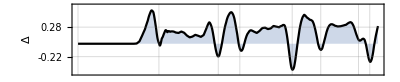
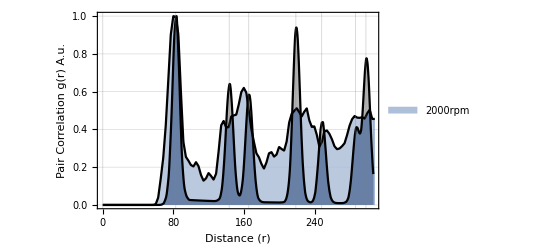
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 79.9868 | 82.6236 | 2.5267 | 183 | 187

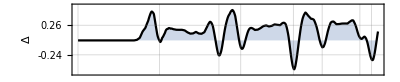
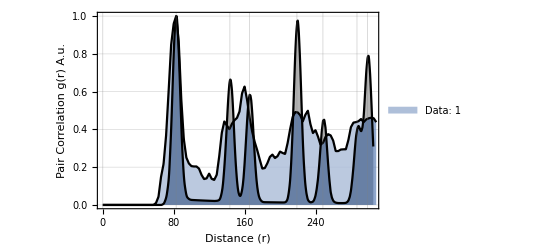
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*  Basic Plot for the Pair Correlation Function                 *)
(*  Returns the Plot of the first-peak normalized g(r) thats Smoothed + Hexatic Lattice *)
(* May take some time to complete:  (1-2 mins for large data sets) *)

PlotPairCorrelationFunction[xylene2000,names->nameList[[1]]]
PlotPairCorrelationFunction@xylene2000
```

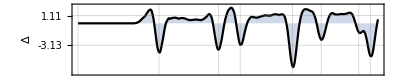
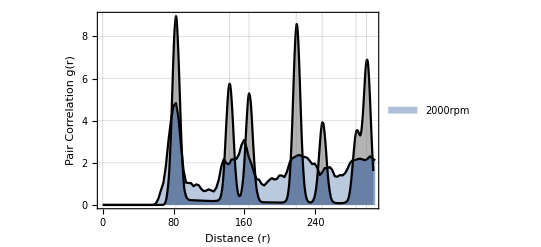
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(* AAdditional Option #1 - absgr *)
(* Remove the normalization of the first peak to see the Absolute Value of g(r)  *)

PlotPairCorrelationFunction[xylene2000,absgr-> True, names->nameList[[1]]]
```

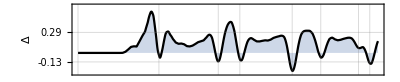
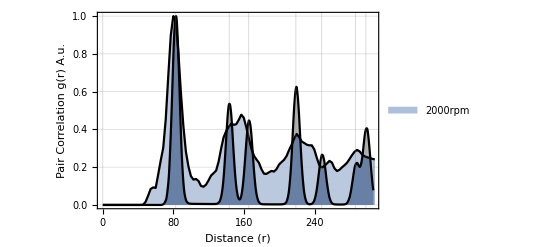
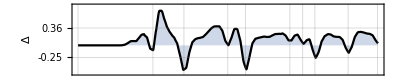
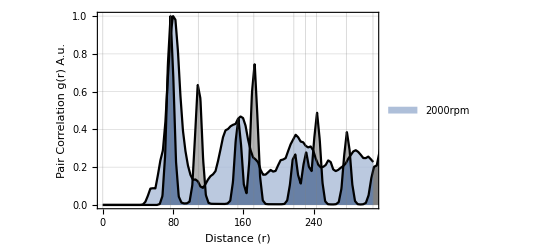
{-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 79.9868 | 82.6236 | 2.5267 | 183 | 187,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Squaratic Lattice) | Expected Disorder
(Squaratic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 79.9868 | 76.8899 | 2.18818 | 183 | 169}

```mathematica
(*     Additional Option #2 - lattice                           *)
(*     Normalizes the x-axis to the expected diameter           *)
(*     Can choose the Reference Lattice:  "hex"  or "square"    *)
PlotPairCorrelationFunction[xylene2000,names->nameList[[1]],lattice-> #]&/@{"hex","square"}
```

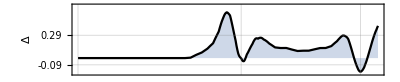
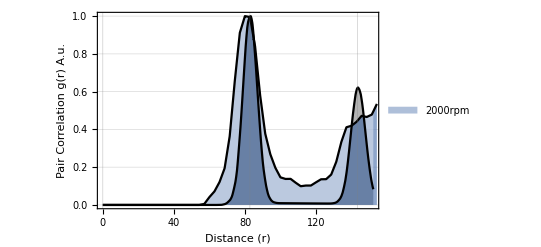
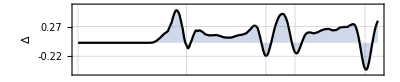
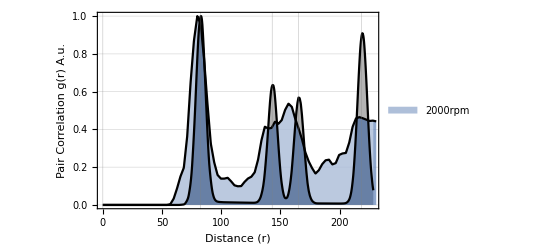
{-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 79.8364 | 82.6236 | 2.5267 | 183 | 187,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 79.8364 | 82.6236 | 2.5267 | 183 | 187}

```mathematica
(*     Additional Option #3 - shells                            *)
(*     Vary the plotting distance with this parameter           *)
(*     Default Value = 4 shells                                 *)

(*    WARNING: If you ever get a divide by zero error (1/0)...   *)
(*     ... the first thing you should do is lower this value!!   *)
(*     Long range distances are bad for sparse data (N<200)      *)

PlotPairCorrelationFunction[xylene2000,names->nameList[[1]],shells-> #]&/@{2,3}
```

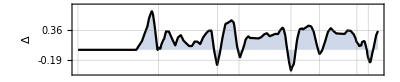
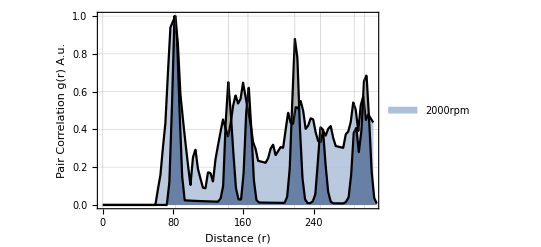
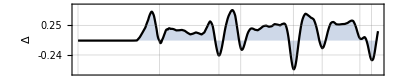
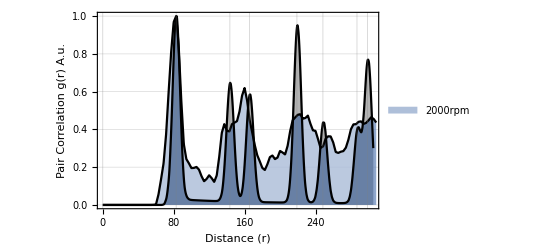
{-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187}

```mathematica
(*     Additional Option #4 - boots                                     *)
(*     Determines the Number of Randomized Displacements used to Smooth *)
(*     Default is 25                                                    *)
PlotPairCorrelationFunction[xylene2000, names->nameList[[1]],boots-> #]&/@{1,200}
```

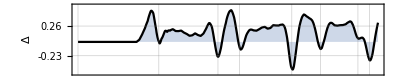
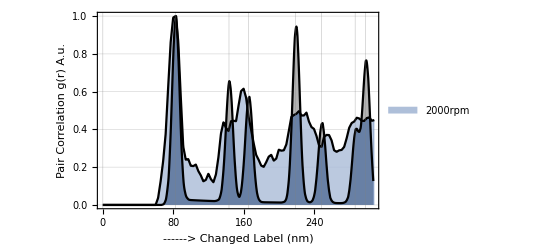
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*     Additional Option #5 - xLabel                    *)
(*     Change the x-axis label to have any string.      *)
PlotPairCorrelationFunction[xylene2000,names->nameList[[1]], xLabel->"------>  Changed Label (nm)"]
```

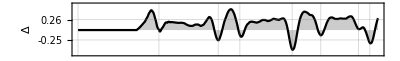
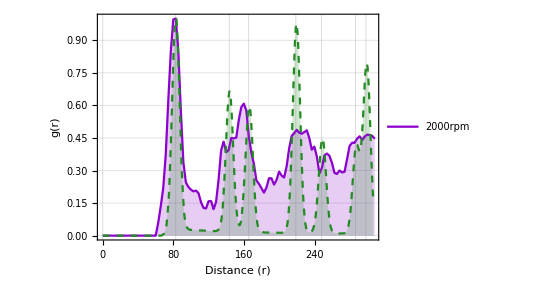
{-Graphics- | 
-Graphics- | }
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
2000rpm | 82.3924 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*     Additional Option #6 - stacked           *)
(*     Use the Green/Purple colour scheme.      *)
PlotPairCorrelationFunction[xylene2000,names->nameList[[1]],stacked->False]
```

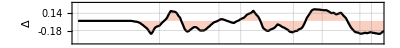
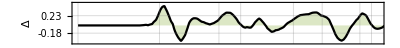
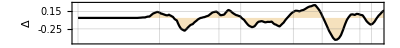
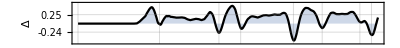
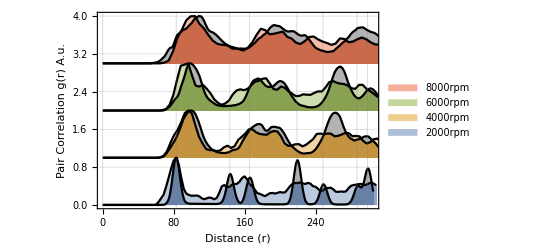
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
8000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187
6000rpm | 96.3248 | 97.0426 | 7.45882 | 131 | 136
4000rpm | 95.9268 | 100.223 | 6.63668 | 126 | 130
2000rpm | 103.756 | 107.439 | 11.4126 | 107 | 114

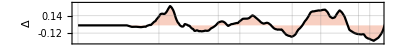
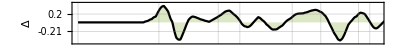
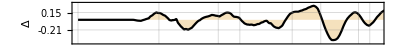
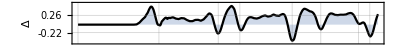
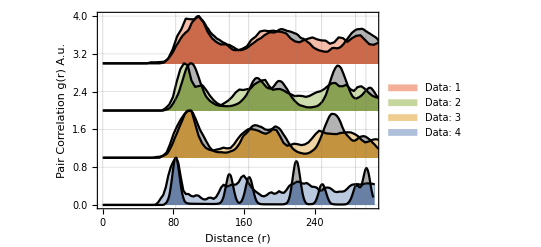
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 82.6931 | 82.6236 | 2.5267 | 183 | 187
Data: 2 | 100.249 | 97.0426 | 7.45882 | 131 | 136
Data: 3 | 91.9299 | 100.223 | 6.63668 | 126 | 130
Data: 4 | 108.904 | 107.439 | 11.4126 | 107 | 114

```mathematica
(*  Call in a List of Data:  *)
(* - Automatically detects multiple {x,y} data and plots it as a stack.  *)
(* - Residual functions at the top are Hexatic Lattice Substractions. *)
(* - All Options above work with this stacked version as well.  *)
(* - Note: table gives names of data in reverse order to the label on the graph. *)

PlotPairCorrelationFunction[xyXyleneList, names->Reverse[nameList]]
 PlotPairCorrelationFunction@xyXyleneList
```

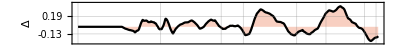
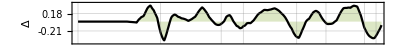
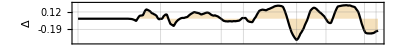
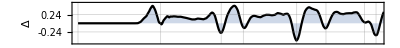
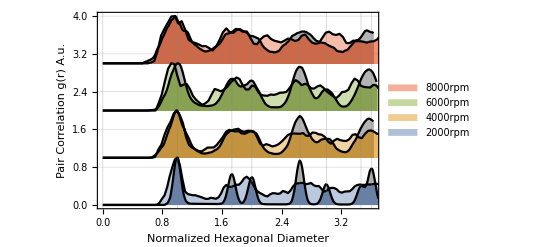
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
8000rpm | 82.6931 | 82.6236 | 2.5267 | 183 | 187
6000rpm | 96.3248 | 97.0426 | 7.45882 | 131 | 136
4000rpm | 92.2932 | 100.223 | 6.63668 | 126 | 130
2000rpm | 103.756 | 107.439 | 11.4126 | 107 | 114

```mathematica
(*  Call in a Normalized List of Data:  *)
(* - Automatically detects multiple {x,y} data and plots it as a stack.  *)
(* - Residual functions at the top are Hexatic Lattice Substractions. *)
(* - All Options above work with this stacked version as well.  *)
(* - Note: Table gives names of data in reverse order to the label on the graph. *)

PlotPairCorrelationFunction[xyXyleneList, normalized->True, names->Reverse[nameList]]
```

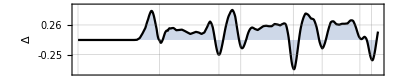
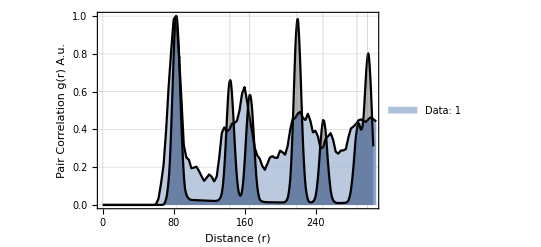
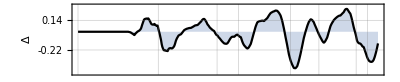
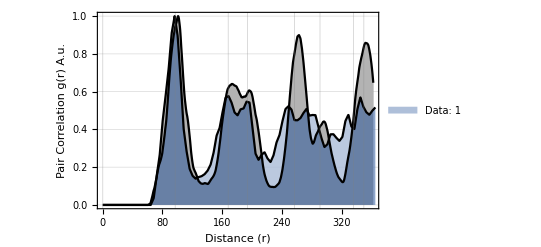
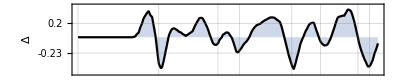
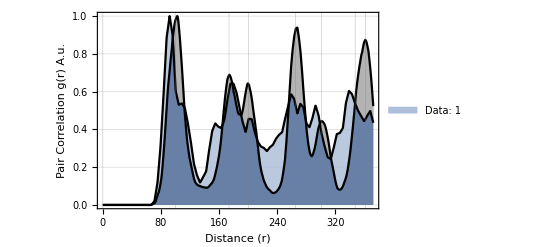
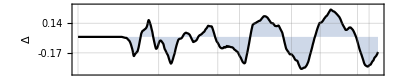
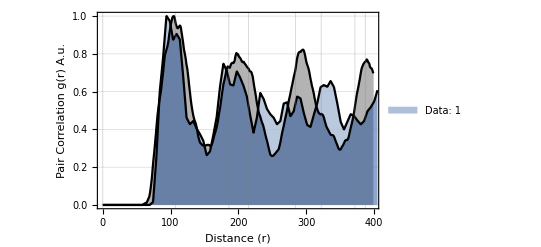
{-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 82.6931 | 82.6236 | 2.5267 | 183 | 187,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 96.3248 | 97.0426 | 7.45882 | 131 | 136,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 91.9299 | 100.223 | 6.63668 | 126 | 130,-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
Data: 1 | 94.2519 | 107.439 | 11.4126 | 107 | 114}

```mathematica
(*     MAP in a List of Data:    *)
(* Returns the Individual Plots for each Configuration in the List *)

(*    Note the:  "/@"  NOT  "@"      *)

PlotPairCorrelationFunction/@xyXyleneList
```

```mathematica
(*    Distance Estimation from: Mathematica's Nearest[] Function   *)

AverageFirstNeighbourDistance/@xyXyleneList
```

{71.3071,82.635,85.4448,89.7071}

```mathematica
(*    Distance Estimation from: First Peak of g(r) - (no smoothing here)  *)

FirstPeakValue/@(PairCorrelationFunction[#]&/@xyXyleneList)
```

{82.8435,96.5914,96.1881,103.78}

```mathematica
(*    Distance Estimation from: Voronoi Areas                      *)
(*    Returns:  { hexatic spacing,  lattice disorder parameter }  *)

ExpectedHexagonalDiameter/@xyXyleneList
```

{{82.6236,2.5267},{97.0426,7.45882},{100.223,6.63668},{107.439,11.4126}}

```mathematica
?PlotPcfDifference
```

"PlotPcfDifference[ PairCorrelationList , OptionsPattern[] ]=Difference Spectrum of PairCorrelationFunction[].  The values for: ref={g(r),r} and func={g(r),r} need to be lists.\nOptionsPattern[]=(xmax→0,normalized→True,shapes→{},stacked→False,names→{},xLabel→{},refIndex→1)\n\nxmax → 1 : Cut-off distance for g(r) where r_max=xmax.\n\nnormalized → True : Automatic rescalling of the x-axis to\n\nshapes → {} : List of Polygons to be used as the Legend Markers where - shapes→{polygon_1, ... , polygon_n} \n\nstacked → False :  Option to overlay curves, or to stack them with an offset.  If stacked→True, it will produce the stacked version.  Multiple PairCorrelationFunction[] can be set with:  func={g(r)_1 , ..., g(r)_n};\n\nxLabel → {}  :  String used to label the distance axis. If xLabel→ToString[Normalized Diameter], the function changes the gridlines to the expected positions of the hexagonal lattice.\n\nrefIndex → 1 : Defines which PairCorrelation[] in the list is chosen as the reference for all others to be subtracted from. "

```mathematica
(*    Allows a comparison of any collection of graphs  *)
(*    Residual functions at the top are substractions relative to first data set.*)


PlotPcfDifference@(PairCorrelationFunction/@xyXyleneList)
```

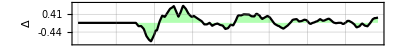
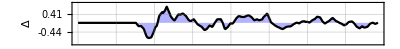
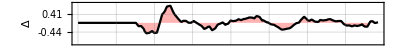
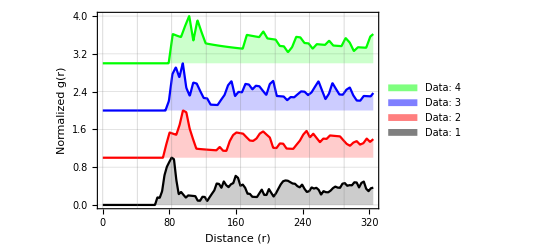

## Bond Order - Angular Orientation of Neighbours

```mathematica
?BondOrderParameter
```

BondOrderParameter[ unBoundedData2D , whichL , OptionsPattern[] ]= Calculates the Bond Order using Delaunay triangulation for neighbour definition.  Defaults are to remove edge particles and apply weighting of (voronoiBondFacet/totalVoronoiPerimeter) to every bond.

OptionsPattern=passVor→{},fast→True,edge->ToString[NoEdge],vorbop→True,box→{},normalized→False,debug→False.

```mathematica
(*  Extract the local bond order parameter for each particle *)
(*  Call using: the data and symmetry number   *)

bop=BondOrderParameter[xylene2000,6];
Mean[bop]
StandardDeviation[bop]
```

0.770507

0.142593

```mathematica
?CoordinationNeighbourCloud
```

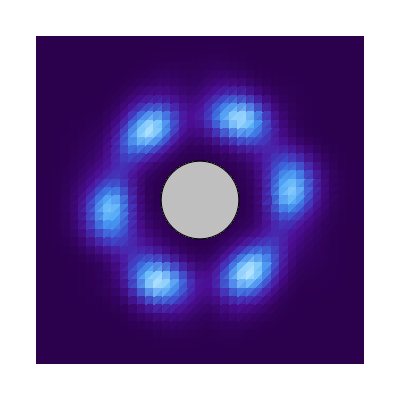
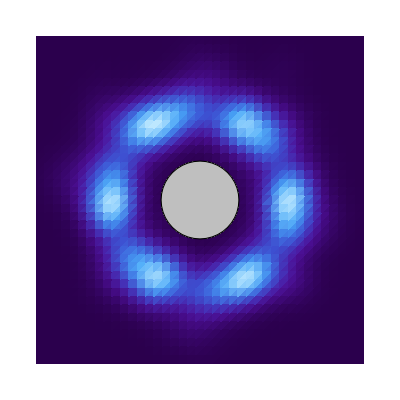
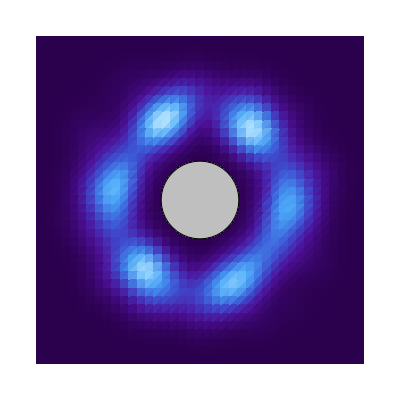
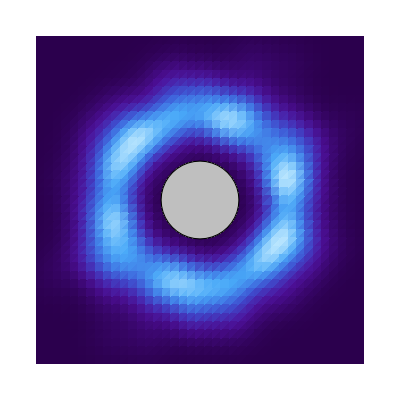

```mathematica
(* Coordination cloud shows the probability of Neighbours relative to each object *) 
(* Similar to the Fourier Transform, except it can be separated by Coordination   *)

(CoordinationNeighbourCloud/@xyXyleneList)[[All,2]]
```

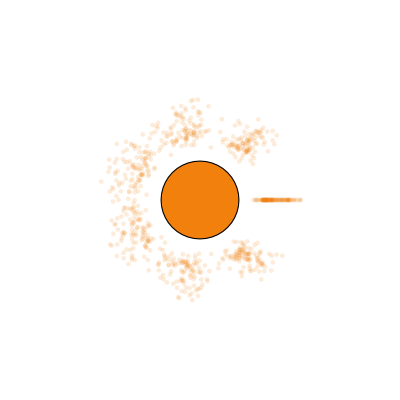
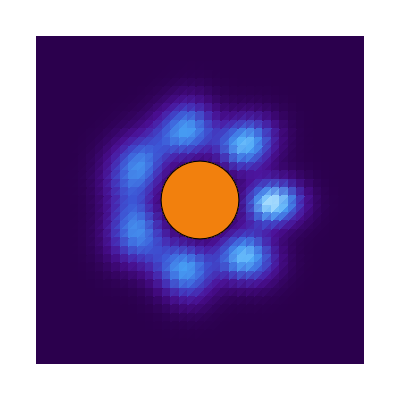
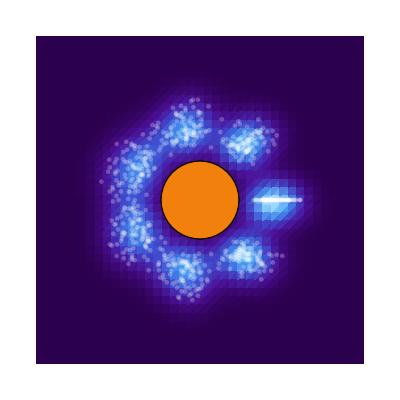

```mathematica
(*   Only select the particles that have 7 neighbours *)

CoordinationNeighbourCloud[xylene2000,coord->7]
```

## Diffraction - Correlation in Inverse Space

```mathematica
?DiffractionPatternFromPosition
```

```mathematica
(*  Plots the Diffraction (Fourier Transform) using a combination of:  *)
(*   ...Mathematica's ImagePeriodogram and ADO FFT (below)  *)

GraphicsRow[DiffractionPatternFromPosition/@xyXyleneList,ImageSize->Large]
```

-Graphics-

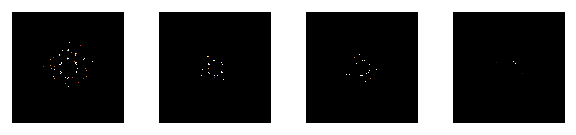

```mathematica
(*  Programmed FFT  *)

GraphicsRow[DiffractionPatternFromPosition[#,annulus-> False]&/@xyXyleneList,ImageSize->Large]
```